```mathematica
PrependTo[$Path, "~/myWork/npmma"];
```

```mathematica
<<Cosmology`
baryonRatio = Omegabh2/OmegaMh2 /. FoMSWG
```

0.171192

```mathematica
(* Keep the baryon/matter ratio fixed *)
```

```mathematica
ff[om_, h_] := Module[{omh2, obh2, tmp},
omh2 = om*h^2;
obh2 =baryonRatio * omh2;
tmp = Join[{OmegaMh2 -> omh2, Omegabh2-> obh2, OmegaDEh2 -> (1-om)*h^2},FoMSWG];
rsEH[tmp]/comdis[z2a[1089.0], tmp]
];
(* Keep the physical baryon density fixed *)
ff1[om_, h_] := Module[{omh, tmp},
omh2 = om*h^2;
tmp = Join[{OmegaMh2 -> omh2, OmegaDEh2 -> (1-om)*h^2},FoMSWG];
rsEH[tmp]/comdis[z2a[1089.0], tmp]
];
```

```mathematica
(* Make the various contour plots and show *)
```

```mathematica
g1 = ContourPlot[ff[om, h], {om, 0.22, 0.32}, {h, 0.66, 0.76}, ContourShading->None, ContourStyle->Dashed, ContourLabels-> True];
g2 = ContourPlot[ff1[om, h], {om, 0.22, 0.32}, {h, 0.66, 0.76}, ContourShading->None, ContourStyle->Directive[Red,Dashed], ContourLabels-> True];
```

```mathematica
g3 = ContourPlot[om*h^2, {om,0.22, 0.32}, {h, 0.66, 0.76}, ContourShading-> None, ContourLabels-> True];
```

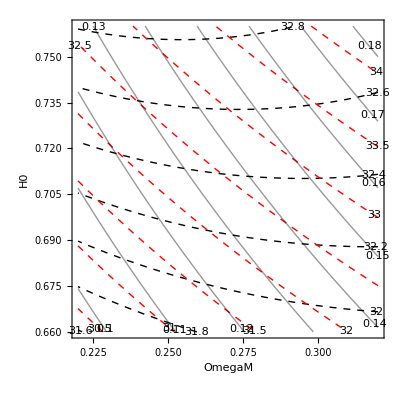

```mathematica
Show[g1, g2,g3,   FrameLabel-> {"OmegaM", "H0"}]
```